```mathematica
250 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
thfi=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\250", "Table"];
```

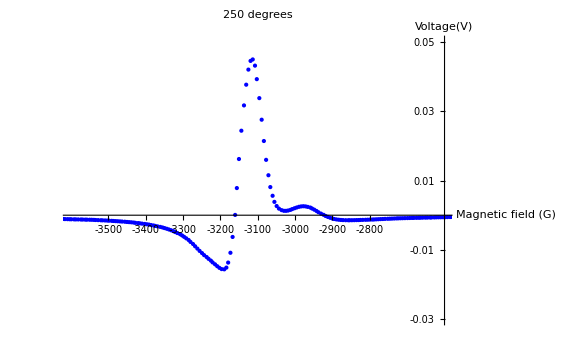

```mathematica
a250=Take[thfi, {5,416}];
pa25=ListPlot[a250,PlotRange->{{-3600,-2600}, {0.05,-0.03}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"250 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.03,-0.01,0.01,0.03,0.05,0.07}}]
```

```mathematica
FindFit[a250, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3160.06,g→-60.4504,v→1014.55}

```mathematica
a1thfi=NonlinearModelFit[a250, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),30<g<70, -2250<v<-250},{{a,-3200},v,g } ,x ]


a1thfi["AdjustedRSquared"]

a1thfi["ParameterTable"]

a1thfi["BestFit"]
```

FittedModel[(19499.4 (3160.05+x))/((3651.23+(«19»+x)^2)^2)]

0.816916

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2157.24] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3160.05 | 0.806522 | -3918.13 | 0.
v | -1013.8 | 47.1239 | -21.5134 | 3.24959×10^-69
g | 60.4254 | 1.62788 | 37.119 | 4.99924×10^-133

(19499.4 (3160.05+x))/((3651.23+(3160.05+x)^2)^2)

```mathematica
Solve[D[(19499.351605290056 (3160.0530374615046+x))/((3651.2278806200543+(3160.0530374615046+x)^2)^2),x]==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-3194.94},{x→-3125.17}}

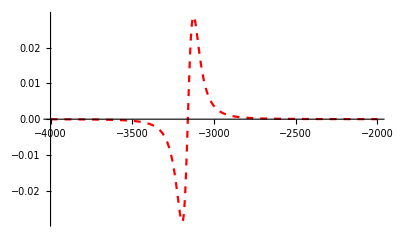

```mathematica
fita250a=Plot[(19499.351605290056 (3160.0530374615046+x))/((3651.2278806200543+(3160.0530374615046+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

```mathematica
pl250=Show[pa25,  fita250a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

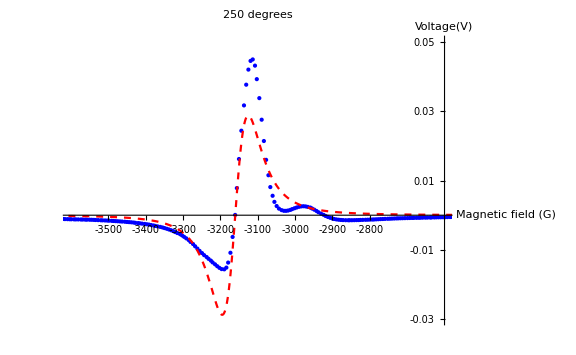

```mathematica
(*gaussian*)


FindFit[a250 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-400},{s,50}},x]
```

{a→-3161.95,v→-235.518,s→43.9202}

```mathematica
a2thtfi=NonlinearModelFit[a250, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<60 ,-900<v<-64},{{a,-3200},v,s} ,x ]


a2thtfi["AdjustedRSquared"]


a2thtfi["ParameterTable"]

a2thtfi["BestFit"]
```

FittedModel[0.00110917 ⅇ^(-0.000259244 (3161.95+x)^2) (3161.95+x)]

0.815105

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2142.22] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3161.95 | 0.837191 | -3776.85 | 0.
v | -235.494 | 8.71438 | -27.0237 | 5.11001×10^-93
s | 43.9168 | 0.842665 | 52.1166 | 1.05392×10^-182

0.00110917 ⅇ^(-0.000259244 (3161.95+x)^2) (3161.95+x)

```mathematica
Solve[D[0.001109168161630178 ⅇ^(-0.00025924354179679925 (3161.9459538382257+x)^2) (3161.9459538382257+x),x]==0,x]
```

{{}}

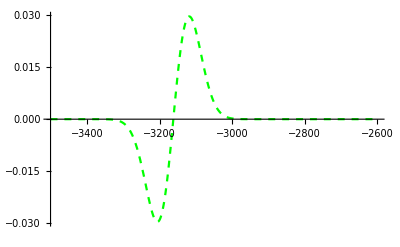

```mathematica
fita250b=Plot[0.001109168161630178 ⅇ^(-0.00025924354179679925 (3161.9459538382257+x)^2) (3161.9459538382257+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

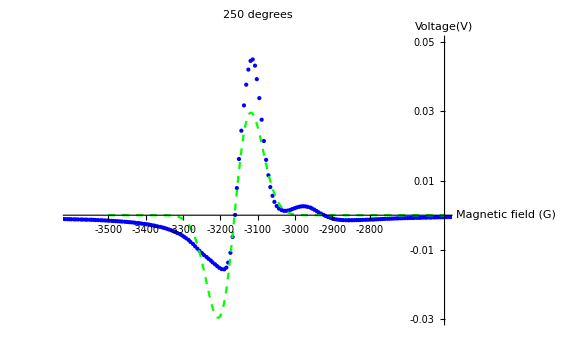

```mathematica
pg250=Show[pa25,  fita250b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

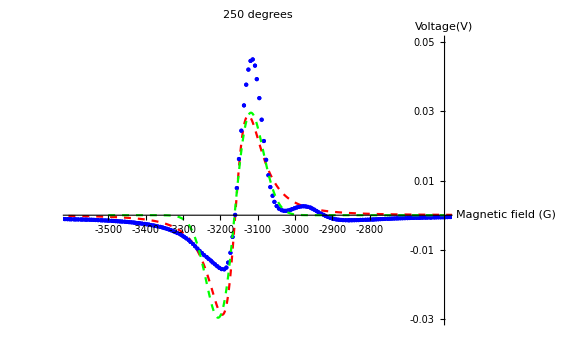

```mathematica
Show[pl250, pg250,ImageSize->Large, AspectRatio->1/GoldenRatio]
```